# Projekt za Računalniška orodja v matematiki

## Analiza NBA ekip med leti 2014 in 2023 4. 7. 2023

## Pridobivanje podatkov

Podatke sem pridobil s strani www.basketball-reference.com.
Za sezone med 2014 in 2023 sem podatke izvozil v csv datoteke, ki so shranjene v Podatki/Ekipe/NBA_{leto}ekipe.cvs

## Povprečje ekip

Spodaj imamo graf ki nam prikazuje povprečje vseh metov, metov za tri točke in metov za dve točki.

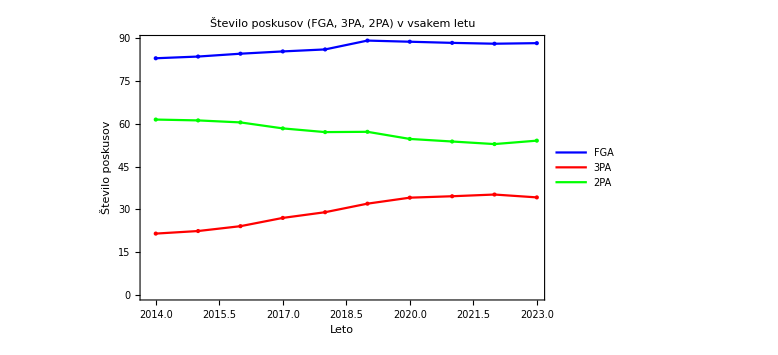

```mathematica
dataDirectory = "C:\\Users\\kosmr\\OneDrive\\Desktop\\ROM\\Podatki\\Ekipe\\";
years = Range[2014, 2023];
totalAttempts = {};
threePointAttempts = {};
twoPointAttempts = {};

Do[
  filePath = FileNameJoin[{dataDirectory, "NBA_" <> ToString[year] <> "ekipe.csv"}];
  data = Import[filePath, "Data"];
  lastRow = Last[data];
  fga = lastRow[[6]];
  threePa = lastRow[[9]];
  twoPa = lastRow[[12]];
  AppendTo[totalAttempts, {year, fga}];
  AppendTo[threePointAttempts, {year, threePa}];
  AppendTo[twoPointAttempts, {year, twoPa}],
  {year, years}
];

ListPlot[
  {totalAttempts, threePointAttempts, twoPointAttempts},
  Joined -> True,
  PlotStyle -> {Directive[Blue, Thick], Directive[Red, Thick], Directive[Green, Thick]},
  Frame -> True,
  FrameLabel -> {"Leto", "Število poskusov"},
  PlotLabel -> "Število poskusov (FGA, 3PA, 2PA) v vsakem letu",
  ImageSize -> Large,
  Epilog -> {
    {Blue, PointSize[Large], Table[Tooltip[Point[totalAttempts[[i]]], totalAttempts[[i]]], {i, Length[totalAttempts]}]},
    {Red, PointSize[Large], Table[Tooltip[Point[threePointAttempts[[i]]], threePointAttempts[[i]]], {i, Length[threePointAttempts]}]},
    {Green, PointSize[Large], Table[Tooltip[Point[twoPointAttempts[[i]]], twoPointAttempts[[i]]], {i, Length[twoPointAttempts]}]}
  },
  PlotLegends -> {"FGA", "3PA", "2PA"}
]
```

S tega grafa lahko sklepamo, da so meti za tri točke postali bolj popularni, saj rastejo in meti za dve točki padajo.

Spodaj imamo graf, ki nam prikazuje poprečje točki, ki so jih dosegale ekipe na tekmo.

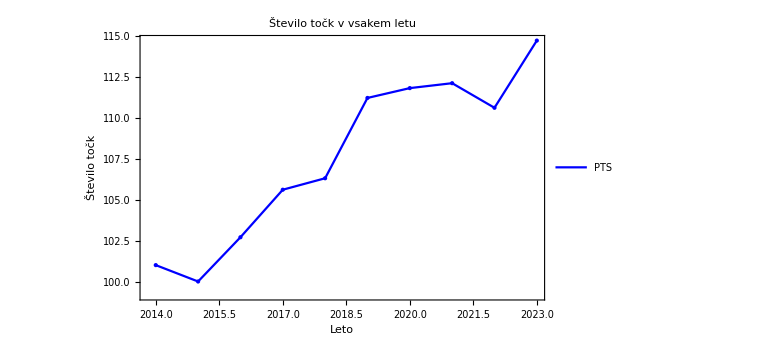

```mathematica
totalPoints = {};
Do[
  filePath = FileNameJoin[{dataDirectory, "NBA_" <> ToString[year] <> "ekipe.csv"}];
  data = Import[filePath, "Data"];
  lastRow = Last[data];
  pts = lastRow[[25]];
  AppendTo[totalPoints, {year, pts}],
  {year, years}
];

ListPlot[
  {totalPoints},
  Joined -> True,
  PlotStyle -> {Directive[Blue, Thick]},
  Frame -> True,
  FrameLabel -> {"Leto", "Število točk"},
  PlotLabel -> "Število točk v vsakem letu",
  ImageSize -> Large,
  Epilog -> {
    {Blue, PointSize[Large], Table[Tooltip[Point[totalPoints[[i]]], totalPoints[[i]]], {i, Length[totalPoints]}]}},
  PlotLegends -> {"PTS"}
]
```

To samo prikazuje, da sedaj ko imamo več poskusov za tri točke imamo tudi več točk na tekmo za vsako ekipo.

## Primerjava ekip

Tabela prikazuje katera ekipa imela največje povprečje točk na tekmo za vsako leto posebaj:

```mathematica
bestTeams = {};

Do[
  filePath = FileNameJoin[{dataDirectory, "NBA_" <> ToString[year] <> "ekipe.csv"}];
  data = Import[filePath, "Data"];
  maxPointsIndex = Position[data[[2 ;; -2, -1]], Max[data[[2 ;; -2, -1]]]][[1, 1]];
  maxPoints = data[[maxPointsIndex + 1, -1]];
  maxPointsTeam = data[[maxPointsIndex + 1, 2]];
  AppendTo[bestTeams, {year, maxPointsTeam, maxPoints}],
  {year, years}
];

TableForm[bestTeams, TableHeadings -> {None, {"Leto", "Ekipa", "Število točk"}}]
```

Leto | Ekipa | Število točk
2014 | Los Angeles Clippers | 107.9
2015 | Golden State Warriors | 110.
2016 | Golden State Warriors | 114.9
2017 | Golden State Warriors | 115.9
2018 | Golden State Warriors | 113.5
2019 | Milwaukee Bucks | 118.1
2020 | Milwaukee Bucks | 118.7
2021 | Milwaukee Bucks | 120.1
2022 | Minnesota Timberwolves | 115.9
2023 | Sacramento Kings | 120.7

Tabela prikazuje katera ekipa imela najboljši procent meta za tri točke na tekmo za vsako leto posebaj:

```mathematica
bestTeams = {};


Do[
  filePath = FileNameJoin[{dataDirectory, "NBA_" <> ToString[year] <> "ekipe.csv"}];
  data = Import[filePath, "Data"];
  maxThreePointPercentageIndex = Position[data[[2 ;; -2, 10]], Max[data[[2 ;; -2, 10]]]][[1, 1]];
  maxThreePointPercentage = data[[maxThreePointPercentageIndex + 1, 10]];
  maxThreePointTeam = data[[maxThreePointPercentageIndex + 1, 2]];
  maxThreePointMade = data[[maxThreePointPercentageIndex + 1, 8]];
  maxThreePointAttempts = data[[maxThreePointPercentageIndex + 1, 9]];
  AppendTo[bestTeams, {year, maxThreePointTeam, maxThreePointMade, maxThreePointAttempts, maxThreePointPercentage}],
  {year, years}
];

TableForm[bestTeams, TableHeadings -> {None, {"Leto", "Najboljša ekipa", "3P", "3PA", "3P%"}}]
```

Leto | Najboljša ekipa | 3P | 3PA | 3P%
2014 | San Antonio Spurs | 8.5 | 21.4 | 0.397
2015 | Golden State Warriors | 10.8 | 27. | 0.398
2016 | Golden State Warriors | 13.1 | 31.6 | 0.416
2017 | San Antonio Spurs | 9.2 | 23.5 | 0.391
2018 | Golden State Warriors | 11.3 | 28.9 | 0.391
2019 | San Antonio Spurs | 9.9 | 25.3 | 0.392
2020 | Utah Jazz | 13.4 | 35.2 | 0.38
2021 | Los Angeles Clippers | 14.3 | 34.7 | 0.411
2022 | Miami Heat | 13.6 | 35.8 | 0.379
2023 | Philadelphia 76ers | 12.6 | 32.6 | 0.387

Tabela prikazuje katera ekipa imela najboljši procent meta za dve točki na tekmo za vsako leto posebaj:

```mathematica
bestTeams = {};

Do[
  filePath = FileNameJoin[{dataDirectory, "NBA_" <> ToString[year] <> "ekipe.csv"}];
  data = Import[filePath, "Data"];
  maxTwoPointPercentageIndex = Position[data[[2 ;; -2, 13]], Max[data[[2 ;; -2, 13]]]][[1, 1]];
  maxTwoPointPercentage = data[[maxTwoPointPercentageIndex + 1, 13]];
  maxTwoPointTeam = data[[maxTwoPointPercentageIndex + 1, 2]];
  maxTwoPointMade = data[[maxTwoPointPercentageIndex + 1, 11]];
  maxTwoPointAttempts = data[[maxTwoPointPercentageIndex + 1, 12]];
  AppendTo[bestTeams, {year, maxTwoPointTeam, maxTwoPointMade, maxTwoPointAttempts, maxTwoPointPercentage}],
  {year, years}
];

TableForm[bestTeams, TableHeadings -> {None, {"Leto", "Najboljša ekipa", "2P", "2PA", "2P%"}}]
```

Leto | Najboljša ekipa | 2P | 2PA | 2P%
2014 | Miami Heat | 30.2 | 54.2 | 0.558
2015 | Los Angeles Clippers | 29.3 | 56.4 | 0.519
2016 | Golden State Warriors | 29.4 | 55.7 | 0.528
2017 | Golden State Warriors | 31.1 | 55.8 | 0.557
2018 | Golden State Warriors | 31.5 | 56.2 | 0.56
2019 | Milwaukee Bucks | 29.9 | 52.9 | 0.565
2020 | Milwaukee Bucks | 29.5 | 52. | 0.567
2021 | Brooklyn Nets | 29. | 51.2 | 0.565
2022 | Denver Nuggets | 29. | 50.4 | 0.575
2023 | Sacramento Kings | 29.8 | 50.9 | 0.586

## Analiza ekipe posebaj

Poišči ekipo

```mathematica
dataDirectory = "C:\\Users\\kosmr\\OneDrive\\Desktop\\ROM\\Podatki\\Ekipe\\";
teams = Import[FileNameJoin[{dataDirectory, "NBA_2014ekipe.csv"}], "Data"][[2 ;; -2, 2]];
years = Range[2014, 2023];
labels = {"Team", "G", "MP", "FG", "FGA", "FG%", "3P", "3PA", "3P%", "2P", "2PA", "2P%", "FT", "FTA", "FT%", "ORB", "DRB", "TRB", "AST", "STL", "BLK", "TOV", "PF", "PTS"};

Manipulate[
    data = {};
    If[team =!= "----",
        data = Table[
            filePath = FileNameJoin[{dataDirectory, "NBA_" <> ToString[i] <> "ekipe.csv"}];
            yearData = Import[filePath, "Data"];
            teamData = Select[yearData[[2 ;; -2]], #[[2]] == team &][[All, 2 ;;]];
            If[Length[teamData] > 0, teamData, {}],
            {i, Min[years], Max[years]}
        ];
    ];

    If[Length[data] > 0,
        pointData = Transpose[{years, data[[All, -1, -1]]}];
        assistData = Transpose[{years, data[[All, -1, 19]]}];
        reboundData = Transpose[{years, data[[All, -1, 18]]}];

        Grid[{
            {ListLinePlot[{pointData, assistData, reboundData},
                PlotLegends -> {"Točke", "Asistence", "Skoki"},
                Frame -> True,
                FrameLabel -> {"Leto", "Vrednost"},
                ImageSize -> 400,
                PlotStyle -> {Directive[Blue, Thick], Directive[Red, Thick], Directive[Green, Thick]},
                Epilog -> {
                           {Blue, PointSize[Large], Tooltip[Point[#], #] & /@ pointData},
                           {Red, PointSize[Large], Tooltip[Point[#], #] & /@ assistData},
                           {Green, PointSize[Large], Tooltip[Point[#], #] & /@ reboundData}
                         }

            ]},
            {Grid[Join[{labels}, Flatten[data, 1]], Frame -> All]}
        }],

        ""
    ],

    {{team, "----", "Ekipa:"}, Prepend[teams, "----"]},

    TrackedSymbols :> {team}
]
```